# Functions and the Map command

## Comprehension Questions

Math 250 - Mathematical Computing
Christopher Hanusa

### 5-1. Before evaluating the following lines of code, anticipate what will be the result will be. After evaluating the code, understand why the output is what it is and compare it with your expectations.

```mathematica
Sin@Pi
```

```mathematica
Map[Sin,{0,Pi/2,Pi,3Pi/2}]
```

{0,1,0,-1}

```mathematica
Map[Sin, Pi]
```

```mathematica
Range@Prime@10
```

```mathematica
Map[Prime,{1,2,4,8}]
```

```mathematica
Map[f,Map[g,Range[5]]]
```

```mathematica
f/@g/@h/@Range[5]
```

```mathematica
Map[PrimeQ,Range[100]]
```

{False,True,True,False,True,False,True,False,False,False,True,False,True,False,False,False,True,False,True,False,False,False,True,False,False,False,False,False,True,False,True,False,False,False,False,False,True,False,False,False,True,False,True,False,False,False,True,False,False,False,False,False,True,False,False,False,False,False,True,False,True,False,False,False,False,False,True,False,False,False,True,False,True,False,False,False,False,False,True,False,False,False,True,False,False,False,False,False,True,False,False,False,False,False,False,False,True,False,False,False}

```mathematica
octothorpe
```

```mathematica
Map[{#,PrimeQ[#]}&,Range[100]]//TableForm
```

1 | False
2 | True
3 | True
4 | False
5 | True
6 | False
7 | True
8 | False
9 | False
10 | False
11 | True
12 | False
13 | True
14 | False
15 | False
16 | False
17 | True
18 | False
19 | True
20 | False
21 | False
22 | False
23 | True
24 | False
25 | False
26 | False
27 | False
28 | False
29 | True
30 | False
31 | True
32 | False
33 | False
34 | False
35 | False
36 | False
37 | True
38 | False
39 | False
40 | False
41 | True
42 | False
43 | True
44 | False
45 | False
46 | False
47 | True
48 | False
49 | False
50 | False
51 | False
52 | False
53 | True
54 | False
55 | False
56 | False
57 | False
58 | False
59 | True
60 | False
61 | True
62 | False
63 | False
64 | False
65 | False
66 | False
67 | True
68 | False
69 | False
70 | False
71 | True
72 | False
73 | True
74 | False
75 | False
76 | False
77 | False
78 | False
79 | True
80 | False
81 | False
82 | False
83 | True
84 | False
85 | False
86 | False
87 | False
88 | False
89 | True
90 | False
91 | False
92 | False
93 | False
94 | False
95 | False
96 | False
97 | True
98 | False
99 | False
100 | False

```mathematica
Map[{#,If[PrimeQ[#],"is prime.","is not prime."]}&,Range[100]]//TableForm
```

1 | is not prime.
2 | is prime.
3 | is prime.
4 | is not prime.
5 | is prime.
6 | is not prime.
7 | is prime.
8 | is not prime.
9 | is not prime.
10 | is not prime.
11 | is prime.
12 | is not prime.
13 | is prime.
14 | is not prime.
15 | is not prime.
16 | is not prime.
17 | is prime.
18 | is not prime.
19 | is prime.
20 | is not prime.
21 | is not prime.
22 | is not prime.
23 | is prime.
24 | is not prime.
25 | is not prime.
26 | is not prime.
27 | is not prime.
28 | is not prime.
29 | is prime.
30 | is not prime.
31 | is prime.
32 | is not prime.
33 | is not prime.
34 | is not prime.
35 | is not prime.
36 | is not prime.
37 | is prime.
38 | is not prime.
39 | is not prime.
40 | is not prime.
41 | is prime.
42 | is not prime.
43 | is prime.
44 | is not prime.
45 | is not prime.
46 | is not prime.
47 | is prime.
48 | is not prime.
49 | is not prime.
50 | is not prime.
51 | is not prime.
52 | is not prime.
53 | is prime.
54 | is not prime.
55 | is not prime.
56 | is not prime.
57 | is not prime.
58 | is not prime.
59 | is prime.
60 | is not prime.
61 | is prime.
62 | is not prime.
63 | is not prime.
64 | is not prime.
65 | is not prime.
66 | is not prime.
67 | is prime.
68 | is not prime.
69 | is not prime.
70 | is not prime.
71 | is prime.
72 | is not prime.
73 | is prime.
74 | is not prime.
75 | is not prime.
76 | is not prime.
77 | is not prime.
78 | is not prime.
79 | is prime.
80 | is not prime.
81 | is not prime.
82 | is not prime.
83 | is prime.
84 | is not prime.
85 | is not prime.
86 | is not prime.
87 | is not prime.
88 | is not prime.
89 | is prime.
90 | is not prime.
91 | is not prime.
92 | is not prime.
93 | is not prime.
94 | is not prime.
95 | is not prime.
96 | is not prime.
97 | is prime.
98 | is not prime.
99 | is not prime.
100 | is not prime.

```mathematica
Map[{ToString[#]<>If[PrimeQ[#]," is prime."," is not prime."]}&,Range[3,100,2]]//TableForm
```

3 is prime.
5 is prime.
7 is prime.
9 is not prime.
11 is prime.
13 is prime.
15 is not prime.
17 is prime.
19 is prime.
21 is not prime.
23 is prime.
25 is not prime.
27 is not prime.
29 is prime.
31 is prime.
33 is not prime.
35 is not prime.
37 is prime.
39 is not prime.
41 is prime.
43 is prime.
45 is not prime.
47 is prime.
49 is not prime.
51 is not prime.
53 is prime.
55 is not prime.
57 is not prime.
59 is prime.
61 is prime.
63 is not prime.
65 is not prime.
67 is prime.
69 is not prime.
71 is prime.
73 is prime.
75 is not prime.
77 is not prime.
79 is prime.
81 is not prime.
83 is prime.
85 is not prime.
87 is not prime.
89 is prime.
91 is not prime.
93 is not prime.
95 is not prime.
97 is prime.
99 is not prime.

```mathematica
99"is not prime"
```

99 is not prime

```mathematica
"is not prime"99
```

99 is not prime

```mathematica
ToString[99]
```

99

```mathematica
StringQ[ToString[99]]
```

True

```mathematica
"A "<>"B "
```

A B

### 5-2. Explain the difference in the outputs between Framed @ {x,y,z} and Framed /@ {x,y,z}.

### 5-3. Use the functions Prime, Map, and Range commands to generate a list of the 100th, 200th, ... up to 2000th prime numbers.

### 5-4. If there is some coordinate data ((x,y)-pairs) in the lists data1, data2, data3, and data4, how can you make a list of scatterplots of these datasets in one line of code?

### 5-5. What do the following functions do?

```mathematica
Prime[10]
```

29

```mathematica
Range[29]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29}

```mathematica
Length[{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29}]
```

29

```mathematica
f1[x_]:=Length[Range[Prime[x]]]
```

```mathematica
Length@Range@Prime@10
```

29

```mathematica
f1[10]
```

29

```mathematica
(Length[Range[Prime[#]]])&[10]
```

29

```mathematica
f2[x_,y_]:={x,y}
```

```mathematica
f2[1,2]
```

{1,2}

```mathematica
{#1,#2}&[5,6]
```

{5,6}

### 5-6. Define a function that takes as input a number n and outputs the 2^n-th prime number

### 5-7. Define a function that takes as input three variables and outputs the sum of the first and third number and divides by the second.

### 5-8. Define a function that takes as input a list and outputs the average value of the entries. Use the function Total.

### 5-9. What is wrong with the following code? It is supposed to take in a number, divide by two, then give the floor of that number. For example, the output for an input of 19 should be Floor[19/2]=Floor[9.5]=9.

```mathematica
fountainOfYouth[x]:=Floor[x/2]
fountainOfYouth(19)
```

## Challenge Questions

### 5-X1. Below is the Mathematica input and output for someone hoping to make a list of square numbers and then append the next square number to the end of that list. How should the code be modified to do these two desired operations?

```mathematica
squares=Table[i^2,{5}];
Append[6^2,%%];
squares
```

### 5-X2. Use various commands that you have learned so far to create the list

```mathematica
{1,1,1,2,4,8,3,9,27,4,16,64,5,25,125,6,36,216,7,49,343,8,64,512,9,81,729,10,100,1000}
```

### 5-X3. Use the Reverse function as necessary to change triangle from Example 5.2.1 into

```mathematica
{{10,9,8,7,6,5,4,3,2,1},
{9,8,7,6,5,4,3,2,1},
{8,7,6,5,4,3,2,1},
{7,6,5,4,3,2,1},
{6,5,4,3,2,1},
{5,4,3,2,1},
{4,3,2,1},
{3,2,1},
{2,1},
{1}}
```

### 5-X4. Use a Table command to create a list of 10 to 100 points that lie in the range [0,100]x[0,100]. Then use the Map command to apply the function Disk to them. Lastly, wrap this whole list in a Graphics command, and you will see your points displayed.

```mathematica
points=Table[RandomInteger[{0,100},2],100]
```

{{91,6},{53,36},{0,3},{100,53},{64,91},{99,13},{64,27},{98,18},{48,69},{98,34},{74,99},{2,42},{60,48},{83,18},{15,29},{98,65},{90,38},{46,16},{86,81},{94,47},{70,11},{92,50},{32,25},{58,71},{25,57},{75,7},{58,13},{45,28},{15,7},{85,16},{84,8},{40,68},{74,99},{74,28},{75,48},{38,28},{25,52},{47,98},{0,42},{55,33},{86,53},{95,87},{50,98},{64,49},{12,89},{55,1},{66,6},{99,49},{86,23},{82,29},{36,29},{37,50},{59,37},{89,20},{96,19},{22,69},{2,96},{38,77},{73,83},{13,1},{65,17},{63,85},{57,88},{90,71},{50,49},{55,72},{41,37},{18,59},{3,20},{23,73},{79,23},{87,74},{81,5},{67,53},{74,83},{24,41},{14,69},{83,87},{52,53},{16,42},{16,72},{84,58},{14,53},{62,41},{46,37},{45,45},{60,63},{79,3},{71,9},{61,67},{22,75},{68,46},{76,46},{68,36},{33,67},{25,56},{20,66},{47,83},{0,46},{41,83}}

```mathematica
Graphics[Map[Disk,points]]
```

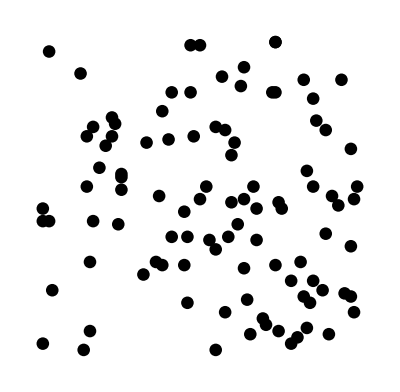

```mathematica
Graphics[Map[Disk[#,2]&,points]]
```

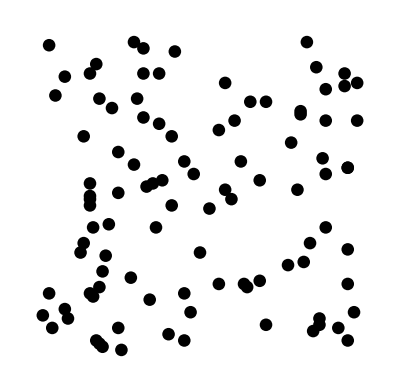

```mathematica
f[pt_]:=Disk[pt,2]
Graphics[Map[f,points]]
```

```mathematica
points=Table[RandomInteger[{0,10},2],10]
```

{{6,7},{10,4},{0,1},{6,7},{9,4},{4,0},{0,5},{8,5},{1,5},{7,4}}

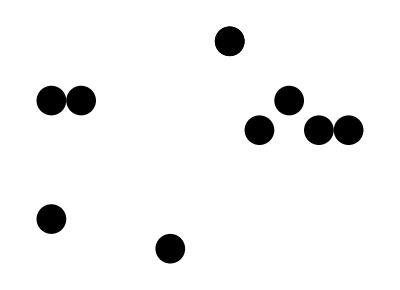
{-Graphics-,-Graphics-}

```mathematica
{
Graphics[Map[Tooltip[Disk[#,.5]]&,points]],
Graphics[Map[Tooltip[Disk[#,.5],#]&,points]]
}
```

```mathematica
(*Graphics[Map[Tooltip[Disk[#,.5],If[#=={0,1},"Winner","Loser!"]]&,points]]*)
```

### 5-X5. Create a function that takes as input a list of numbers, interprets the list as a sequence of two-dimensional points (coordinate pairs), and outputs a scatterplot of these points. You may find the function Partition helpful.

```mathematica
list=RandomInteger[{1,20},100]
```

{17,12,6,12,19,2,18,20,14,5,7,7,5,11,18,8,19,3,20,15,16,15,17,14,5,10,15,14,10,9,1,17,12,16,17,11,11,20,15,10,9,5,1,8,8,6,13,7,16,9,11,3,1,18,20,4,19,20,20,14,1,9,11,11,15,1,17,5,4,11,5,3,19,18,12,16,15,8,10,6,11,16,11,19,4,8,20,19,13,17,16,19,7,20,13,1,16,14,3,1}

```mathematica
coords=Partition[list,2]
```

{{17,12},{6,12},{19,2},{18,20},{14,5},{7,7},{5,11},{18,8},{19,3},{20,15},{16,15},{17,14},{5,10},{15,14},{10,9},{1,17},{12,16},{17,11},{11,20},{15,10},{9,5},{1,8},{8,6},{13,7},{16,9},{11,3},{1,18},{20,4},{19,20},{20,14},{1,9},{11,11},{15,1},{17,5},{4,11},{5,3},{19,18},{12,16},{15,8},{10,6},{11,16},{11,19},{4,8},{20,19},{13,17},{16,19},{7,20},{13,1},{16,14},{3,1}}

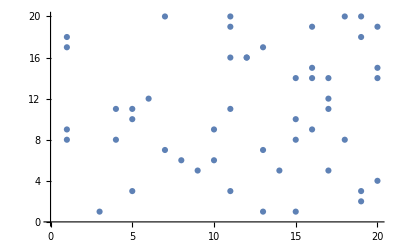

```mathematica
ListPlot[coords]
```

Scatterplot takes in a list of numbers, breaks them into pairs of numbers, imagines that they are coordinates, and creates a scatterplot of these points.

```mathematica
scatterplot[l1_]:=ListPlot[Partition[l1,2]]
```

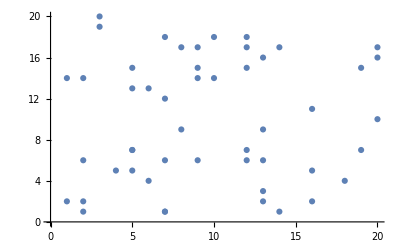

```mathematica
scatterplot@RandomInteger[{1,20},100]
```

### 5-X6. Create a function that takes as input a number n and gives as output an image with of n random points in the range [0,100]x[0,100]. (Similar to 5-X3 above.)

I needed to create 2n random numbers instead of n random numbers because scatterplot (defined above) needs two entries for each coordinate pair.

```mathematica
makelovenotwar[n_]:=scatterplot@RandomReal[{0,100},2n] (* Use 2n not n *)
```

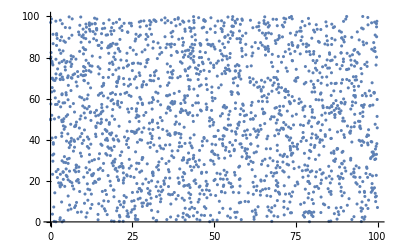

```mathematica
makelovenotwar[2000]
```